Your Title Here

```mathematica
f1=203;f2=303;
f3[x_]:=-1769*x^2-66.42*x+513.1;
f4[x_]:=-1718*x^2+2955*x-703.6;
f5[x_]:=-1756*x^2+1718*x+52.36;
f6[x_]:=-7097*x^2+14370*x-6648;
```

```mathematica
diagram=Show[
Graphics@{Directive[Darker[Blue,0.5],Opacity@0.35],Rectangle[{0,100},{1,625}]},
Plot[#1,Evaluate@Flatten@{x,#2},PlotStyle->None,Filling->#3,FillingStyle->#4]&@@@{{Piecewise[{{f1,x<0.6},{f2,0.6<x}}],{0,1},100,GrayLevel@0.85},{f3[x],{0,0.4},f1,RGBColor[1,1,0.4]},{f4[x],{0.4,0.6},f1,RGBColor[0.4,1,1]},{f5[x],{0.6,0.8},f2,RGBColor[0.4,1,1]},{f6[x],{0.8,1},f2,RGBColor[1,1,0.4]}},
Plot[#1,Evaluate@Flatten@{x,#2},PlotStyle->{Thick,Black}]&@@@{{f1,{0,0.6}},{f2,{0.6,1}},{f3[x],{0,0.4}},{f4[x],{0.4,0.6}},{f5[x],{0.6,0.8}},{f6[x],{0.8,1}}},
Graphics@{Thick,Line[{{0.6,100},{0.6,f5[0.6]}}]},
PlotRange->{{0,1},{100,625}},PlotRangePadding->None,Axes->None,Frame->True,FrameLabel->{"mole fraction B","temperature (°C)"},LabelStyle->{17,Black},ImageSize->{425,400},AspectRatio->Full];
```

```mathematica
lines=Graphics@{Text[Framed[Style[Subscript["f",#1],18],Background->LightRed,FrameStyle->None,FrameMargins->Tiny,RoundingRadius->10],#2]&@@@{
{1,{0.15,f1}},{2,{0.92,f2}},{3,{0.2,f3[0.2]}},{4,{0.5,f4[0.5]}},{5,{0.7,f5[0.7]}},{6,{0.9,f6[0.9]}}}};
```

```mathematica
colorA=RGBColor[0.75,0,0];
colorB=RGBColor[0,0.5,0];
colorAB=RGBColor[1,0.44,0];
colorL=RGBColor[0,0,0.5];
```

```mathematica
labels=Graphics@{
Text[Style[Column[{Row@{#1," +"},#2},Center],15],#3]&@@@{
{Style["solid A",colorA],Style[Row@{"solid ",Subscript["A",2],Subscript["B",3]},colorAB],{0.3,150}},
{Style["solid B",colorB],Style[Row@{"solid ",Subscript["A",2],Subscript["B",3]},colorAB],{0.8,200}},
{Style["solid A",colorA],Style["liquid",colorL],{0.12,350}},
{Style["liquid",colorL],Style[Row@{"solid ",Subscript["A",2],Subscript["B",3]},colorAB],{0.51,230}},
{Style["liquid",colorL],Style[Row@{"solid ",Subscript["A",2],Subscript["B",3]},colorAB],{0.697,330}},
{Style["solid B",colorB],Style["liquid",colorL],{0.92,330}}},
Text[Style["liquid",colorL,14],{0.5,550}]
};
```

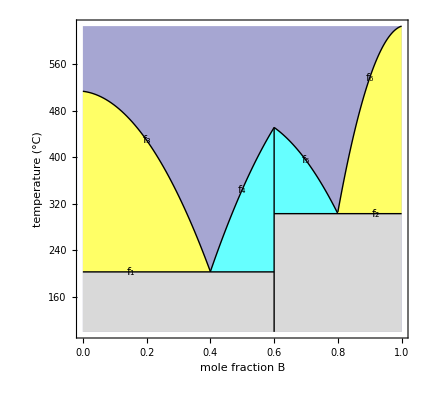

```mathematica
Show[diagram,lines]
```

```mathematica
{f4[0.6],f5[0.6]}
```

{450.92,451.}

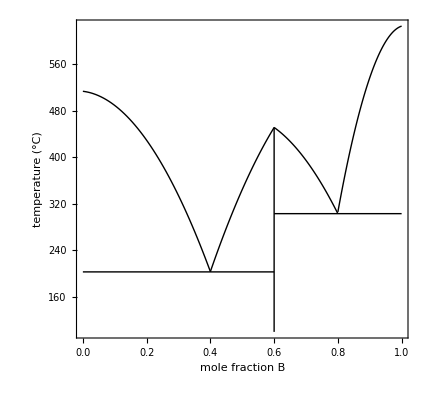

```mathematica
Show[
Plot[#1,Evaluate@Flatten@{x,#2},PlotStyle->{Thick,Black}]&@@@{{f1,{0,0.6}},{f2,{0.6,1}},{f3[x],{0,0.4}},{f4[x],{0.4,0.6}},{f5[x],{0.6,0.8}},{f6[x],{0.8,1}}},
Graphics@{Thick,Line[{{0.6,100},{0.6,f5[0.6]}}]},
PlotRange->{{0,1},{100,625}},PlotRangePadding->None,Axes->None,Frame->True,FrameLabel->{"mole fraction B","temperature (°C)"},LabelStyle->{17,Black},ImageSize->{425,400},AspectRatio->Full]
```

```mathematica
Manipulate[
Module[{Q1,Q2,py},
Q1=heat+100;Q2=heat;
py=Sort[{Q1,Which[px<0.6,f1,px>0.6,f2,px==0.6,450],Q2}][[2]];

If[px<0.6∧py<f1,step=1];
If[px>0.6∧py<f2,step=2];
If[px==0.6∧py<450,step=3];

If[px<0.6∧py==f1,step=10];
If[px>0.6∧py==f2,step=20];
If[px==0.6∧py==450,step=30];

Grid@{{Show[diagram,Epilog->{PointSize@0.027,Point[{px,py}]}],Text@Style[Grid[{{"step =",step},{},{"Q_1 =",Q1},{"Q_2 =",Q2},{"py =",py}}],18]}}
],
Grid[{
{Control[{{px,0.2,"mole fraction B"},0,1,0.05,Appearance->"Labeled"(*,Enabled->If[step==3∨step==30,False,True]*)}],
Button["reset to initial conditions",heat=20],SpanFromLeft},
{Control[{{heat,20,"heat added (kJ)"},0,500,1,Appearance->"Labeled"}],
Control[{{label,False,"labels"},{True,False}}],
Control[{{region,False,"regions"},{True,False}}],
Control[{{step,1},0,40,None}]}
},Alignment->Left],
SaveDefinitions->True]
```

```mathematica
ypoint=heat+100;
ypoint2=heat;
```

```mathematica
(*BarChart[{1,2,3,4},ChartStyle->{Red,Blue,Green,Purple},Frame->{{True,False},{True,False}},ImageSize->{175,400},AspectRatio->Full]*)
```

```mathematica
(*Show[diagram,If[label,labels,Graphics[]],If[region,regions,Graphics[]],Epilog->{PointSize@0.027,Point[{px,py}]}]*)
```





```mathematica
(*R1=px<0.6∧py<f1;
R2=0.6<px∧py<f2;
R3=px≤0.4∧f1<py≤f3[px];
R4=0.4<px<0.6∧f1<py≤f4[px];
R5=0.6<px≤0.8∧f2<py≤f5[px];
R6=0.8<px∧f2<py≤f6[px];
R7=(px≤0.4∧f3[px]<py)∨(0.4<px≤0.6∧f4[px]<py)∨(0.6<px≤0.8∧f5[px]<py)∨(0.8<px∧f6[px]<py);
RA=px<0.6∧py==f1;
RB=0.6<px∧py==f2;
RC=px==0.6∧py≤f5[0.6];

regions=Graphics@{
Text[Framed[Style[Subscript["R",#1],18,If[#2,{Bold,Blue},Black]],Background->If[#2,Lighter[Orange,0.5],White],FrameStyle->None,FrameMargins->Tiny,RoundingRadius->10],{First@#3,0.5*Total@Last@#3}]&@@@{
{1,R1,{0.3,{90,f1}}},{2,R2,{0.8,{100,f2}}},{3,R3,{0.2,{f1,f3[0.2]}}},{4,R4,{0.53,{f1,f4[0.53]}}},{5,R5,{0.68,{f2,f5[0.68]}}},{6,R6,{0.92,{f2,f6[0.92]}}},{7,R7,{0.5,{550,550}}},{"A",RA,{0.3,{f1,f1}}},{"B",RB,{0.8,{f2,f2}}},{"C",RC,{0.6,{f1,f2}}}}};*)
```

Resize Images

Rotate and Zoom in 3D

Drag Locators

Create and Delete Locators

Slider Zoom

Gamepad Controls

Automatic Animation

Bookmark Animation

Contributed by: XXXX